## 1 step: R -> B -> P1

### Ratios

```mathematica
Clear[ksyn,ki,kd1,kd2,k1,k2,kis,p1,p2]
k1 = kd1/kD1;
k2 = kd2/kD2;
L1 = u1*kD1;
L2 = u2*kD2;
kd2 = δ*kd1;
kp = ω*kd1;
kdp = ρ*kp;
kin = kd1*μ;
krec = kd1*τ;
```

### Equations

```mathematica
Clear[e1,e2,e3,e4,e5,e6,e7,e8]
e1 = -k1*L1*r+kd1*b1+kd1*p1+krec*ϕ1==0;(*R*)
e2 = k1*L1*r-kd1*b1-kp*b1+kdp*p1==0;(*B1*)
e3 = kp*b1-kdp*p1-kd1*p1-kin*p1==0;(*P1*)
e4 = kin*p1-krec*ϕ1==0;
(**)
e5 = -k2*L2*r+kd2*b2+kd2*p2+krec*ϕ2==0;(*R*)
e6 = k2*L2*r-kd2*b2-kp*b2+kdp*p2==0;(*B1*)
e7 = kp*b2-kdp*p2-kd2*p2-kin*p2==0;(*P1*)
e8 = kin*p2-krec*ϕ2==0;
```

### Solutions

```mathematica
Clear[ex1]
solx1=Solve[{e1,e2,e3,e4,r+b1+p1+ϕ1==1},{r,b1,p1,ϕ1}][[1]];
r1 = ((p1)/.solx1);
solx2=Solve[{e5,e6,e7,e8,r+b2+p2+ϕ2==1},{r,b2,p2,ϕ2}][[1]];
r2 = ((p2)/.solx2);
ex1[δ_,τ_,μ_,ω_,ρ_]=FullSimplify[Limit[(r1/r2)/.{u1->u,u2->u},u->Infinity]]
```

1+((-1+δ) τ)/(μ ω+τ (1+μ+ω+ρ ω))

1+((-1+δ) τ)/(μ ω+τ (1+μ+ω))

## 2 step: R -> B -> P1 -> P2

### Ratios

```mathematica
Clear[ksyn,ki,kd1,kd2,k1,k2,kis,p1,p2]
k1 = kd1/kD1;
k2 = kd2/kD2;
L1 = u1*kD1;
L2 = u2*kD2;
kd2 = δ*kd1;
kp = ω*kd1;
kdp = ρ*kp;
kin = kd1*μ;
krec = kd1*τ;
```

### Equations

```mathematica
Clear[e1,e2,e3,e4,e5,e6,e7,e8]
e1 = -k1*L1*r+kd1*b1+kd1*p1+kd1*q1+krec*ϕ1==0;(*R*)
e2 = k1*L1*r-kd1*b1-kp*b1+kdp*p1==0;(*B1*)
e3 = kp*b1-kdp*p1-kd1*p1-kp*p1+kdp*q1==0;(*P1*)
e4 = kp*p1-kdp*q1-kd1*q1-kin*q1==0;
e5 = kin*q1-krec*ϕ1==0;
(**)
e6 = -k2*L2*r+kd2*b2+kd2*p2+kd2*q2+krec*ϕ2==0;(*R*)
e7 = k2*L2*r-kd2*b2-kp*b2+kdp*p2==0;(*B1*)
e8 = kp*b2-kdp*p2-kd2*p2-kp*p2+kdp*q2==0;(*P1*)
e9 = kp*p2-kdp*q2-kd2*q2-kin*q2==0;
e10 = kin*q2-krec*ϕ2==0;
```

### Solutions

```mathematica
Clear[ex2]
solx1=Solve[{e1,e2,e3,e4,e5,r+b1+p1+q1+ϕ1==1},{r,b1,p1,q1,ϕ1}][[1]];
r1 = ((p1+q1)/.solx1);
solx2=Solve[{e6,e7,e8,e9,e10,r+b2+p2+q2+ϕ2==1},{r,b2,p2,q2,ϕ2}][[1]];
r2 = ((p2+q2)/.solx2);
ex2[δ_,τ_,μ_,ω_,ρ_]=FullSimplify[Limit[(r1/r2)/.{u1->u,u2->u},u->Infinity]]
```

((1+μ+ω+ρ ω) (δ (δ+μ) τ+(2 δ (1+ρ)+μ (2+ρ)) τ ω+(μ+(1+ρ+ρ^2) τ) ω^2))/((δ+μ+ω+ρ ω) (μ ω^2+τ (1+μ+μ (2+ρ) ω+ω (2+ω+ρ (2+ω+ρ ω)))))

((1+μ+ω) (δ (δ+μ) τ+2 (δ+μ) τ ω+(μ+τ) ω^2))/((δ+μ+ω) (μ ω^2+τ (μ+2 μ ω+(1+ω)^2)))

## 3 step: R -> B -> P1 -> P2 -> P3

### Ratios

```mathematica
Clear[ksyn,ki,kd1,kd2,k1,k2,kis,p1,p2]
k1 = kd1/kD1;
k2 = kd2/kD2;
L1 = u1*kD1;
L2 = u2*kD2;
kd2 = δ*kd1;
kp = ω*kd1;
kdp = ρ*kp;
kin = kd1*μ;
krec = kd1*τ;
```

### Equations

```mathematica
Clear[e1,e2,e3,e4,e5,e6,e7,e8,e9,e10,e11,e12]
e1 = -k1*L1*r+kd1*b1+kd1*p1+kd1*q1+kd1*f1+krec*ϕ1==0;(*R*)
e2 = k1*L1*r-kd1*b1-kp*b1+kdp*p1==0;(*B1*)
e3 = kp*b1-kdp*p1-kd1*p1-kp*p1+kdp*q1==0;(*P1*)
e4 = kp*p1-kdp*q1-kd1*q1-kp*q1+kdp*f1==0;
e5 = kp*q1-kdp*f1-kd1*f1-kin*f1==0;
e6 = kin*f1-krec*ϕ1==0;
(**)
e7 = -k2*L2*r+kd2*b2+kd2*p2+kd2*q2+kd2*f2+krec*ϕ2==0;(*R*)
e8 = k2*L2*r-kd2*b2-kp*b2+kdp*p2==0;(*B1*)
e9 = kp*b2-kdp*p2-kd2*p2-kp*p2+kdp*q2==0;(*P1*)
e10 = kp*p2-kdp*q2-kd2*q2-kp*q2+kdp*f2==0;
e11= kp*q2-kdp*f2-kd2*f2-kin*f2==0;
e12 = kin*f2-krec*ϕ2==0;
```

### Solutions

```mathematica
Clear[ex3]
solx1=Solve[{e1,e2,e3,e4,e5,e6,r+b1+p1+q1+f1+ϕ1==1},{r,b1,p1,q1,f1,ϕ1}][[1]];
r1 = ((p1+q1+f1)/.solx1);
solx2=Solve[{e7,e8,e9,e10,e11,e12,r+b2+p2+q2+f2+ϕ2==1},{r,b2,p2,q2,f2,ϕ2}][[1]];
r2 = ((p2+q2+f2)/.solx2);
ex3[δ_,τ_,μ_,ω_,ρ_]=Limit[(r1/r2)/.{u1->u,u2->u},u->Infinity];
```

## 4 step: R -> B -> P1 -> P2 -> P3 -> P4

### Ratios

```mathematica
Clear[ksyn,ki,kd1,kd2,k1,k2,kis,p1,p2]
k1 = kd1/kD1;
k2 = kd2/kD2;
L1 = u1*kD1;
L2 = u2*kD2;
kd2 = δ*kd1;
kp = ω*kd1;
kdp = ρ*kp;
kin = kd1*μ;
krec = kd1*τ;
```

### Equations

```mathematica
Clear[e1,e2,e3,e4,e5,e6,e7,e8]
e1 = -k1*L1*r+kd1*b1+kd1*p1+kd1*q1+kd1*f1+kd1*g1+krec*ϕ1==0;(*R*)
e2 = k1*L1*r-kd1*b1-kp*b1+kdp*p1==0;(*B1*)
e3 = kp*b1-kdp*p1-kd1*p1-kp*p1+kdp*q1==0;(*P1*)
e4 = kp*p1-kdp*q1-kd1*q1-kp*q1+kdp*f1==0;
e5 = kp*q1-kdp*f1-kd1*f1-kp*f1+kdp*g1==0;
e6 = kp*f1-kdp*g1-kd1*g1-kin*g1==0;
e7 = kin*g1-krec*ϕ1==0;
(**)
e8 = -k2*L2*r+kd2*b2+kd2*p2+kd2*q2+kd2*f2+kd2*g2+krec*ϕ2==0;(*R*)
e9 = k2*L2*r-kd2*b2-kp*b2+kdp*p2==0;(*B1*)
e10 = kp*b2-kdp*p2-kd2*p2-kp*p2+kdp*q2==0;(*P1*)
e11 = kp*p2-kdp*q2-kd2*q2-kp*q2+kdp*f2==0;
e12 = kp*q2-kdp*f2-kd2*f2-kp*f2+kdp*g2==0;
e13 = kp*f2-kdp*g2-kd2*g2-kin*g2==0;
e14 = kin*g2-krec*ϕ2==0;
```

### Solutions

```mathematica
Clear[ex4]
solx1=Solve[{e1,e2,e3,e4,e5,e6,e7,r+b1+p1+q1+f1+g1+ϕ1==1},{r,b1,p1,q1,f1,g1,ϕ1}][[1]];
r1 = ((p1+q1+f1+g1)/.solx1);
solx2=Solve[{e8,e9,e10,e11,e12,e13,e14,r+b2+p2+q2+f2+g2+ϕ2==1},{r,b2,p2,q2,f2,g2,ϕ2}][[1]];
r2 = ((p2+q2+f2+g2)/.solx2);
ex4[δ_,τ_,μ_,ω_,ρ_,u_]=(r1/r2)/.{u1->u,u2->u,kd1->1};
```

## 5 step: R -> B -> P1 -> P2 -> P3 -> P4 -> P5

### Ratios

```mathematica
Clear[ksyn,ki,kd1,kd2,k1,k2,kis,p1,p2]
k1 = kd1/kD1;
k2 = kd2/kD2;
L1 = u1*kD1;
L2 = u2*kD2;
kd2 = δ*kd1;
kp = ω*kd1;
kdp = ρ*kp;
kin = kd1*μ;
krec = kd1*τ;
```

### Equations

```mathematica
Clear[e1,e2,e3,e4,e5,e6,e7,e8,e9,e10,e11,e12,e13,e14,e15,e16]
e1 = -k1*L1*r+kd1*b1+kd1*p1+kd1*q1+kd1*f1+kd1*g1+kd1*h1+krec*ϕ1==0;(*R*)
e2 = k1*L1*r-kd1*b1-kp*b1+kdp*p1==0;(*B1*)
e3 = kp*b1-kdp*p1-kd1*p1-kp*p1+kdp*q1==0;(*P1*)
e4 = kp*p1-kdp*q1-kd1*q1-kp*q1+kdp*f1==0;
e5 = kp*q1-kdp*f1-kd1*f1-kp*f1+kdp*g1==0;
e6 = kp*f1-kdp*g1-kd1*g1-kp*g1+kdp*h1==0;
e7 = kp*g1-kdp*h1-kd1*h1-kin*h1==0;
e8 = kin*h1-krec*ϕ1==0;
(**)
e9 = -k2*L2*r+kd2*b2+kd2*p2+kd2*q2+kd2*f2+kd2*g2+kd2*h2+krec*ϕ2==0;(*R*)
e10 = k2*L2*r-kd2*b2-kp*b2+kdp*p2==0;(*B1*)
e11 = kp*b2-kdp*p2-kd2*p2-kp*p2+kdp*q2==0;(*P1*)
e12 = kp*p2-kdp*q2-kd2*q2-kp*q2+kdp*f2==0;
e13 = kp*q2-kdp*f2-kd2*f2-kp*f2+kdp*g2==0;
e14 = kp*f2-kdp*g2-kd2*g2-kp*g2+kdp*h2==0;
e15 = kp*g2-kdp*h2-kd2*h2-kin*h2==0;
e16 = kin*h2-krec*ϕ2==0;
```

### Solutions

```mathematica
Clear[ex5]
solx1=Solve[{e1,e2,e3,e4,e5,e6,e7,e8,r+b1+p1+q1+f1+g1+h1+ϕ1==1},{r,b1,p1,q1,f1,g1,h1,ϕ1}][[1]];
r1 = ((p1+q1+f1+g1+h1)/.solx1);
solx2=Solve[{e9,e10,e11,e12,e13,e14,e15,e16,r+b2+p2+q2+f2+g2+h2+ϕ2==1},{r,b2,p2,q2,g2,f2,h2,ϕ2}][[1]];
r2 = ((p2+q2+f2+g2+h2)/.solx2);
ex5[δ_,τ_,μ_,ω_,ρ_,u_]=(r1/r2)/.{u1->u,u2->u,kd1->1};
```

## Compare

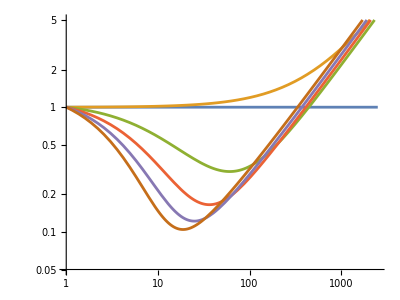

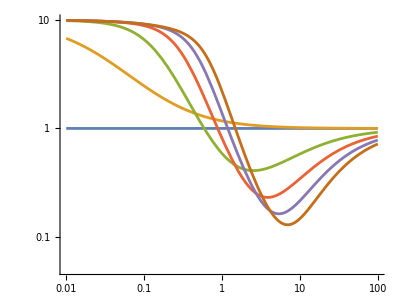

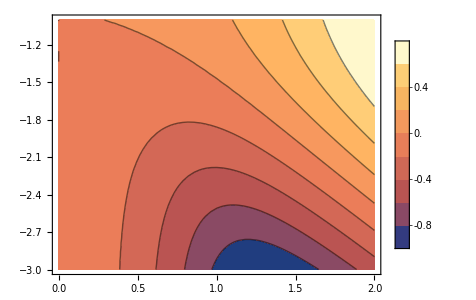

```mathematica
ωE = 1;
γE = 0.05;
δE = 10;
τE = 0.001;
ωE = 10;
ρE = 0;
Show[LogLogPlot[{1,ex1[δ,τE,γE,ωE,ρE],ex2[δ,τE,γE,ωE,ρE],ex3[δ,τE,γE,ωE,ρE],ex4[δ,τE,γE,ωE,ρE,1000],ex5[δ,τE,γE,ωE,ρE,100]},{δ,1,2500},PlotRange->{0.05,5},AspectRatio->0.75],TextStyle->FontSize->20]
Show[LogLogPlot[{1,ex1[δE,τE,γE,ω,ρE],ex2[δE,τE,γE,ω,ρE],ex3[δE,τE,γE,ω,ρE],ex4[δE,τE,γE,ω,ρE,1000],ex5[δE,τE,γE,ω,ρE,1000]},{ω,1/100,100},PlotRange->{0.05,10},AspectRatio->0.75],TextStyle->FontSize->20]
Show[ContourPlot[Log10[ex5[10^δ,10^τ,γE,ωE,ρE,1000]],{δ,0,2},{τ,-3,-1},PlotLegends->True,AspectRatio->0.75,PlotRange->All,Contours->8],TextStyle->FontSize->20]
```